```mathematica
Clear[d1]
```

```mathematica
d1[ω_,δ_,t_,ϵ_]:=d1[ω,δ,t,ϵ]=Module[{J=Inverse[(ω+ⅈ*δ-ϵ)IdentityMatrix[1]],B:=Inverse[(ω+ⅈ*δ-ϵ)IdentityMatrix[1]],T=t*IdentityMatrix[1]},Do[J=Inverse[IdentityMatrix[1]-B.T.J.T].B,50000];J=J]
```

```mathematica
d1[0,0.0001,1,0]
```

{{0.-1.01351 ⅈ}}

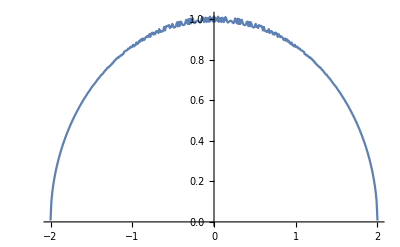

```mathematica
Show[ListLinePlot[Table[{ω,-Im[d1[ω,0.0001,1,0][[1,1]]]},{ω,Range[-2,2,0.01]}]]]
```

```mathematica
Clear[β]
```

```mathematica
β[ω_,δ_,t_,ϵ_,γ_]:=
β[ω,δ,t,ϵ,γ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->t]
```

```mathematica
T1[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
T1[1]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
(*Import leads *)
```

```mathematica
Lead=Table[ToExpression[Import["~/Downloads/PhD_new/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,γ_]:=LEFT[ω,δ,t,ϵ,γ]=(*Module[{J=Inverse[β[ω,δ,t,ϵ,γ]],B:=Inverse[β[ω,δ,t,ϵ,γ]],T=T1[1]},Do[J=Inverse[IdentityMatrix[1]-B.T.J.T].B,5000];J=J]*)Lead[[ω*100+1]]
```

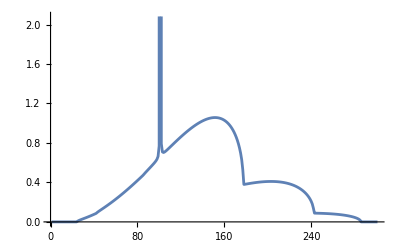

```mathematica
ListLinePlot[Table[-LEFT[ω,0.0001,1,0,1][[1,1]]//Im,{ω,0,3,0.01}]]
```

```mathematica
(*Or Generate leads using recursive algorithm*)
```

```mathematica
g[ω_,δ_,t_,ϵ_,γ_]:= Inverse[β[ω,δ,t,ϵ,γ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,γ_]:=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ,γ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ,γ].T1[t]].g[ω,δ,t,ϵ,γ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,γ_]:=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ,γ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ,γ].T1[t]].g[ω,δ,t,ϵ,γ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,γ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ,γ].TT[t].SR[ω,δ,t,ϵ,γ].TT[t]].SL[ω,δ,t,ϵ,γ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,γ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ,γ].TT[t].SL[ω,δ,t,ϵ,γ].TT[t]].SR[ω,δ,t,ϵ,γ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,γ_]:= IL[ω,δ,t,ϵ,γ]-ConjugateTranspose[IL[ω,δ,t,ϵ,γ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,γ_]:= IR[ω,δ,t,ϵ,γ]-ConjugateTranspose[IR[ω,δ,t,ϵ,γ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,γ_]:= SR[ω,δ,t,ϵ,γ].TT[t].IL[ω,δ,t,ϵ,γ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,γ_]:= Gnonlocal[ω,δ,t,ϵ,γ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,γ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,γ_]:=Abs[Tr[gdd[ω,δ,t,ϵ,γ].TT[t].grr[ω,δ,t,ϵ,γ].TT[t]-TT[t].GNON[ω,δ,t,ϵ,γ].TT[t].GNON[ω,δ,t,ϵ,γ]]]
```

```mathematica
tr[1,0.0001,1,0,0.01]
```

3.

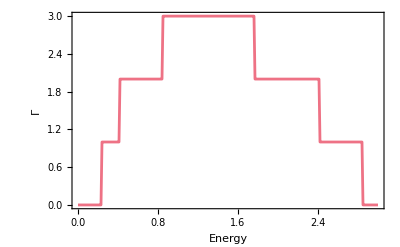

```mathematica
ListLinePlot[ParallelTable[{ω,tr[ω,0.0001,1,0,0.1]},{ω,Range[0,3,0.01]}],Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0.5,0.6}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}]
```

```mathematica
Configuraional Averaging
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
impurity[ω_,δ_,t_,ϵ_,ϵ1_,n_,γ_]:=Module[{b=β[ω,δ,t,ϵ,γ]},ReplacePart[b,Table[F[RandomSample[{RandomInteger[{1,14}]},1]]//Flatten,n]->ω+ⅈ*δ-ϵ1]]
```

```mathematica
CAvg[ω_,δ_,t_,ϵ_,ϵ1_,n_,num_,size_,γ_]:= Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{},
(* Distribution of impurities inside the device region *)
lista={RandomSample[Join[Table[impurity[ω,0.0001,1,0,ϵ1,1,γ],num],Table[impurity[ω,0.0001,1,0,0,1,γ],size-num]]]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0,γ]},Do[J=Inverse[IdentityMatrix[14]-Inverse[lista[[1,ζ]]].ConjugateTranspose[Tin].J.Tin].Inverse[lista[[1,ζ]]],{ζ,1,size}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0,γ].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0,γ].T.sl1.T].SR[ω,0.0001,1,0,γ];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0,γ].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0,γ],tr[ω,0.0001,1,0,γ],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
Table[Table[{ω,Mean[ParallelTable[CAvg[ω,0.0001,1,0,0.5,1,x,100,0.1],1000]]},{ω,Range[0,3,0.01]}],{x,10,70,10}]
```

{1.68937,1.52475,1.3644,1.21626,1.07396,0.981493,0.882166}

```mathematica
(* Size= 100 , M = Number of configurations considered for averaging = 2500 *)
```

```mathematica
avg= Compile[{ω,num},ParallelTable[CAvg[ω,0.0001,1,0,0.5,1,num,100],2500],CompilationOptions->{"ExpressionOptimization" -> True},Parallelization->True,CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
(*Generate Configurational average spectras and export! 
num = number of impurities inside the device *)
```

```mathematica
Table[Export["~/PhD_new/PhD/substrate_ca_7agnr_"<>ToString[x]<>"_.dat",Table[{ω,Mean[ParallelTable[CAvg[ω,0.0001,1,0,0.5,1,x,100,0.1],1000]]},{ω,Range[0,3,0.01]}]],{x,Range[5,80,10]}]
```

{~/PhD_new/PhD/substrate_ca_7agnr_5_.dat,~/PhD_new/PhD/substrate_ca_7agnr_15_.dat,~/PhD_new/PhD/substrate_ca_7agnr_25_.dat,~/PhD_new/PhD/substrate_ca_7agnr_35_.dat,~/PhD_new/PhD/substrate_ca_7agnr_45_.dat,~/PhD_new/PhD/substrate_ca_7agnr_55_.dat,~/PhD_new/PhD/substrate_ca_7agnr_65_.dat,~/PhD_new/PhD/substrate_ca_7agnr_75_.dat}

```mathematica
(*Interpolation (machine learning??)*)
```

```mathematica
(*Import generated averages from above section*)
```

```mathematica
transmission = Table[Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[X]<>".dat"],{X,Range[5,85,6]}]
```

{{{0.,2.79841×10^-7},{0.01,2.72438×10^-7},{0.02,2.76055×10^-7},{0.03,2.8154×10^-7},293,{2.97,1.58019×10^-7},{2.98,1.34547×10^-7},{2.99,1.15807×10^-7},{3.,1.01074×10^-7}},12,{1}}
 |  |  |  |

```mathematica
Dimensions[transmission]
```

{14,301,2}

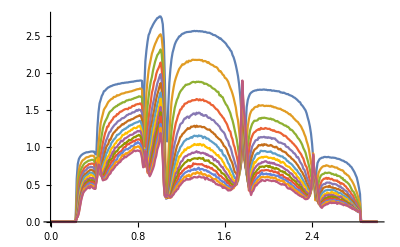

```mathematica
ListLinePlot[transmission]
```

```mathematica
trainingset[ω_]:=Table[5+10*(n-1)->transmission[[n]][[ω*100+1,2]],{n,Range[1,14,1]}]
```

```mathematica
data[num_,ω_]:=Module[{P},P=Predict[trainingset[ω],Method->"LinearRegression"]; P[num]]
```

```mathematica
(*This allows us to generate average specta for continuous number of impurities *)
```

```mathematica
Mean[ParallelTable[CAvg[1,0.0001,1,0,0.5,1,50,100],5000]]//AbsoluteTiming
```

{0.043947,CAvg[1,0.0001,1,0,0.5,1,50,100]}

```mathematica
ParallelTable[data[x,1.2],{x,1,85}]
```

{2.1197,2.09899,2.08513,2.07714,2.06383,2.04923,2.03527,2.02131,2.00791,1.99399,1.98003,1.96606,1.9521,1.93259,1.92362,1.90485,1.89624,1.87712,1.86325,1.84938,1.84037,1.82636,1.81197,1.79842,1.78406,1.76618,1.75614,1.7426,1.72458,1.71071,1.70067,1.68674,1.66911,1.65877,1.64484,1.63053,1.61364,1.60294,1.58897,1.57498,1.56104,1.54707,1.53311,1.51657,1.50515,1.49119,1.47701,1.46306,1.44931,1.43534,1.42138,1.40563,1.39344,1.37789,1.36402,1.35154,1.33629,1.32242,1.30954,1.29469,1.2817,1.26775,1.25371,1.23981,1.22585,1.21184,1.19791,1.18395,1.16988,1.15601,1.14206,1.12828,1.11412,1.10019,1.08623,1.07228,1.05832,1.04428,1.03041,1.01635,1.02215,0.988418,0.975738,0.960624,0.946668}

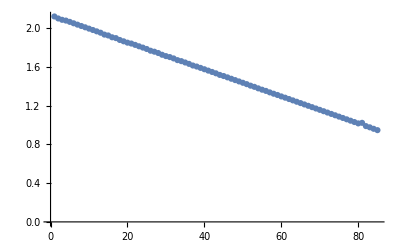

```mathematica
ListPlot[%50]
```

```mathematica
Table[{X,Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[X]<>".dat"][[121]][[2]]},{X,Range[5,85,6]}]
```

{{5,2.51559},{11,2.09529},{17,1.77006},{23,1.51341},{29,1.32478},{35,1.15011},{41,1.0194},{47,0.911323},{53,0.813863},{59,0.736825},{65,0.651904},{71,0.608596},{77,0.557658},{83,0.512468}}

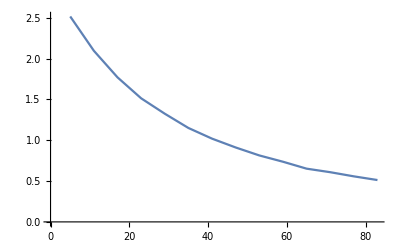

```mathematica
ListPlot[%53,Joined->True]
```

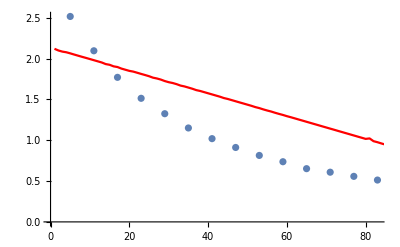

```mathematica
Show[ListPlot[%53],ListPlot[%50,PlotStyle->Red,Joined->True]]
```

```mathematica
%39
```

{{5,2.51559},{7,2.35725},{9,2.22219},{11,2.09529},{13,1.96939},{15,1.87142},{17,1.77006},{19,1.68211},{21,1.59245},{23,1.51341},{25,1.43574},{27,1.38754},{29,1.32478},{31,1.26152},{33,1.20764},{35,1.15011},{37,1.09977},{39,1.07481},{41,1.0194},{43,0.986417},{45,0.957193},{47,0.911323},{49,0.889966},{51,0.845224},{53,0.813863},{55,0.791116},{57,0.759266},{59,0.736825},{61,0.697025},{63,0.687513},{65,0.651904},{67,0.62965},{69,0.624792},{71,0.608596},{73,0.584907},{75,0.577781},{77,0.557658},{79,0.552758},{81,0.524299},{83,0.512468},{85,0.50709}}

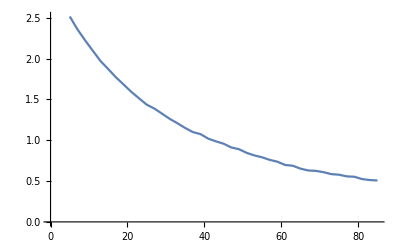

```mathematica
ListPlot[%56,Joined->True]
```

```mathematica
Export["data_ml.dat",%37]
```

data_ml.dat

```mathematica
Export["data_ml_2.dat",%39]
```

data_ml_2.dat

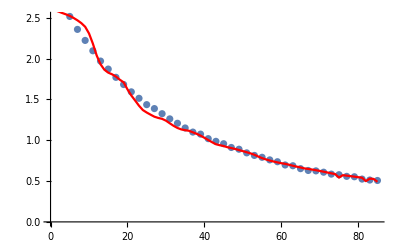

```mathematica
Show[ListPlot[%39],ListPlot[%37,PlotStyle->Red,Joined->True]]
```

```mathematica
Length[%26]
```

50

```mathematica
Interpolation[%26]
```

InterpolatingFunction[…]

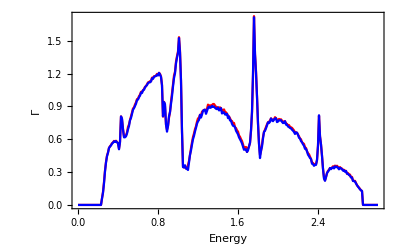

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test55.dat"],PlotStyle->Red,Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}],ListLinePlot[Table[{ω,data[55,ω]},{ω,Range[0,3,0.01]}],PlotStyle->Blue]]
```

```mathematica
Misfit Function
```

```mathematica
(* Import interpolated averages *)
```

```mathematica
transmission100= Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[X]<>".dat"],{X,Range[5,85,2]}]
```

{{{0.,2.79841×10^-7},{0.01,2.72438×10^-7},{0.02,2.76055×10^-7},{0.03,2.8154×10^-7},{0.04,2.86312×10^-7},{0.05,2.93608×10^-7},{0.06,3.05841×10^-7},{0.07,3.15627×10^-7},{0.08,3.3353×10^-7},283,{2.92,4.55387×10^-7},{2.93,3.50822×10^-7},{2.94,2.79217×10^-7},{2.95,2.26938×10^-7},{2.96,1.88087×10^-7},{2.97,1.58019×10^-7},{2.98,1.34547×10^-7},{2.99,1.15807×10^-7},{3.,1.01074×10^-7}},39,{1}}
 |  |  |  |

```mathematica
(* Generate input spectra using kubo formula *)
```

```mathematica
input= Table[ParallelTable[{ω,inputspectra[ω,0.5,100]},{ω,Range[0,3,0.01]}],100]
```

{{{0.,2.8×10^-7},{0.01,5.16712×10^-8},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},283,{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}},98,{1}}
 |  |  |  |

```mathematica
Misfit[x_,y_,n_]:=Module[{m5 = input[[n]]},ρ1:= Table[Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-transmission100[[ξ]][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,41}]; 
Transpose[Join[{Range[5,85,2]},{ρ1}]]]
```

```mathematica
Misfit[2.75,0.,11]
```

{{5,1.11817},{7,0.91521},{9,0.757861},{11,0.63398},{13,0.535305},{15,0.45536},{17,0.390342},{19,0.337636},{21,0.293519},{23,0.257535},{25,0.228839},{27,0.205541},{29,0.187088},{31,0.171541},{33,0.161349},{35,0.153364},{37,0.146054},{39,0.142945},{41,0.139989},{43,0.140467},{45,0.14104},{47,0.142151},{49,0.145398},{51,0.148378},{53,0.153118},{55,0.158354},{57,0.164478},{59,0.169579},{61,0.175676},{63,0.181392},{65,0.187352},{67,0.19376},{69,0.199789},{71,0.207357},{73,0.214103},{75,0.219639},{77,0.226812},{79,0.232498},{81,0.239189},{83,0.246054},{85,0.251049}}

```mathematica
(*Number of impurities obtained from the inversion for given input spectra*)
```

```mathematica
Table[Misfit[2.75,0,n][[Position[Misfit[2.75,0,n],Min[Misfit[2.75,0,n]]][[1,1]]]],{n,100}]
```

{{47,0.137902},{45,0.14688},{45,0.134238},{43,0.133453},{43,0.136068},{43,0.123634},{41,0.144587},{43,0.143977},{43,0.142133},{39,0.125987},{41,0.139989},{43,0.116007},{41,0.154824},{43,0.124223},{41,0.124322},{39,0.128029},{47,0.125809},{43,0.133357},{43,0.110319},{43,0.129125},{43,0.116526},{43,0.14218},{47,0.163235},{45,0.131681},{45,0.13698},{41,0.15125},{45,0.145527},{47,0.132367},{43,0.126166},{39,0.127407},{45,0.131273},{45,0.125321},{47,0.152259},{47,0.147723},{45,0.132715},{45,0.132664},{43,0.129684},{39,0.119487},{43,0.153135},{45,0.127782},{37,0.15048},{41,0.137563},{41,0.119651},{43,0.143111},{45,0.153866},{41,0.135766},{41,0.146521},{41,0.131101},{41,0.103069},{41,0.118465},{45,0.135073},{45,0.133369},{45,0.117376},{43,0.124894},{45,0.143631},{45,0.151417},{47,0.129575},{45,0.131588},{47,0.155161},{43,0.132751},{45,0.124034},{41,0.146746},{47,0.124189},{49,0.131882},{45,0.162905},{47,0.175007},{43,0.13813},{41,0.109266},{47,0.113629},{41,0.13005},{43,0.127215},{47,0.15577},{45,0.117928},{39,0.113305},{43,0.133559},{43,0.132052},{43,0.137933},{43,0.13655},{43,0.115283},{43,0.140312},{41,0.146326},{41,0.134415},{45,0.133353},{43,0.132024},{41,0.151885},{43,0.115376},{41,0.13483},{47,0.118475},{43,0.13614},{45,0.104488},{43,0.128015},{41,0.107363},{43,0.138926},{43,0.14259},{45,0.136347},{43,0.140149},{43,0.131321},{41,0.133123},{43,0.11857},{43,0.121488}}

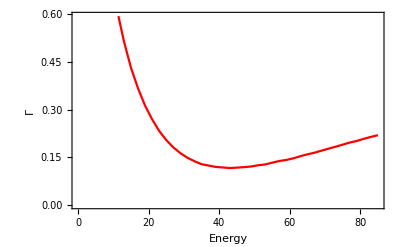

```mathematica
ListPlot[Misfit[2.75,0,12],Joined->True,PlotStyle->Red,Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}]
```

```mathematica
Export["line.dat",Table[{50,x},{x,0,0.02,0.00001}]]
```

line.dat

```mathematica
f1[y_,start_,stop_]:=f1[y,start,stop]= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=s[xstart,xstop,ystart,ystop]=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[concentration_]:=dist[concentration]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,2],s[1,100,6,9],s[1,100,13,14]],concentration],RandomSample[Join[s[1,100,3,5],s[1,100,10,12]],15-concentration]],First],10000]
```

```mathematica
dist[10][[1]]
```

{{2,1},{14,9},{15,1},{42,9},{55,13},{70,7},{75,9},{80,6},{96,9},{100,2}}

```mathematica
Clear[f,CA]
```

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,γ_,concentration_,number_,unitcell_]:=
Inverse[Module[{J=β[ω,δ,t,ϵ,γ]},
Do[J=Module[{m=unitcell},
If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,concentration}];J]]
```

```mathematica
β[0,0.0001,1,0,0]//MatrixForm
```

```mathematica
dist[10][[1]]
```

{{7,2},{12,6},{25,3},{29,4},{41,2},{53,3},{60,9},{84,14},{91,5},{92,10}}

```mathematica
f[0,0.0001,1,0,1,0,10,1,7]//Inverse
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,γ_,concentration_,number_]:= Module[{J2=LEFT[ω,δ,t,ϵ,γ]},
recurs=Module[{J1=LEFT[ω,δ,t,ϵ,γ]},
Do[
J1=Inverse[IdentityMatrix[14]-f[ω,δ,t,ϵ,ϵ1,γ,concentration,number,unitcell].ConjugateTranspose[T1[t]].J1.T1[t]].f[ω,δ,t,ϵ,ϵ1,γ,concentration,number,unitcell],{unitcell,1,100}];J1];ir=Inverse[IdentityMatrix[14]-J2.TT[1].recurs.TT[1]].J2;il=Inverse[IdentityMatrix[14]-recurs.TT[1].J2.TT[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TT[1].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]];TRA]
```

```mathematica
Monitor[Table[Table[Mean[ParallelTable[CA[w,0.0001,1,0,0.5,0,x,n],{n,2000}]],{w,Range[0.2,3,0.1]}],{x,5,12,2}],w]
```

{{0.744358,0.820301,0.856267,0.879258,0.897366,0.907669,0.91541,0.921564,0.927946,0.93099,0.933056,0.937865,0.940429,0.940188,0.940945,0.937593},{0.666236,0.760524,0.812565,0.842768,0.860486,0.872049,0.88577,0.890779,0.898654,0.9049,0.907741,0.915207,0.917797,0.918253,0.918663,0.914383},{0.591755,0.70325,0.75967,0.796348,0.825995,0.841253,0.853062,0.862485,0.872795,0.878039,0.881932,0.892498,0.895107,0.900222,0.895668,0.887364},{0.515787,0.647922,0.719324,0.755392,0.791155,0.808619,0.824029,0.839463,0.842244,0.856708,0.864505,0.869951,0.870545,0.875381,0.87369,0.862207}}

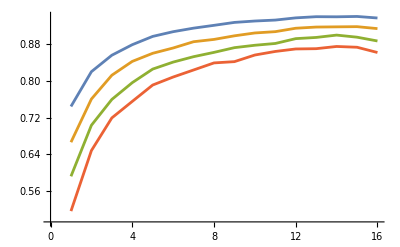

```mathematica
ListLinePlot[%125]
```

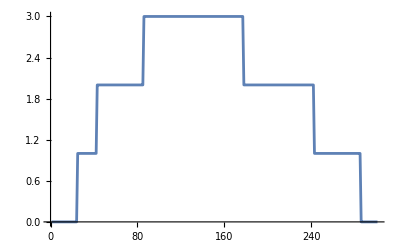

```mathematica
Table[CA[w,0.0001,1,0,0,0,14,100],{w,Range[0,3,0.01]}]//ListLinePlot
```

```mathematica
Table[-Im[LEFT[w,0.0001,1,0,0][[1,1]]],{w,Range[0,3,0.01]}]//ListLinePlot
```

-Graphics-

```mathematica
ListLinePlot[Monitor[Table[{ω,CA[ω,0.0001,1,0,0,0,10,100,50,1]},{ω,Range[0,3,0.01]}],ω]]
```

$Aborted